## Three-dimensional trial wave function. Effect of donor position

## 3D - Trial wavefunction:

```mathematica
ClearAll["Global`*"]

t1=AbsoluteTime[];
well=60.;
dz=1.;
border=200.;
lw=Floor[well/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well,dz];lz=Length[z];

x=0.1;
vmax=0.7*1.587*x;
v=0.0*z;
v⟦Range[lb]⟧=v⟦-Range[lb]⟧=vmax;
hom=7.62559/0.096;
ϵ=10.6*55.26349406*10^-4;

ψmax=100.;
tol=10^-10;
rd=Range[0.,220.,20.];
rd=Append[rd,230.];
elist3d=wavefn3d=bohrrad3d=0.0*rd;
λ=199.;dλ=-1.;
 
i1[λ_,z_]:=π (λ Abs[z]+λ^2/2.) * Exp[-2. Abs[z]/λ];
i2[λ_,z_]:=-π*(z)*Exp[-2. Abs[z]/λ];
i3[λ_,z_]:= π (Abs[z]/λ-3./2. )*Exp[-2. Abs[z]/λ];
i4[λ_,z_]:=π λ *Exp[-2. Abs[z]/λ];

Do[
α=i1[λ,z-rd⟦j⟧];
β= 2.*i2[λ,z-rd⟦j⟧];
i3λ=i3[λ,z-rd⟦j⟧];
i4λ=i4[λ,z-rd⟦j⟧];

energy=-0.030;de=0.0001;
γ=i3λ+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);
ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i<lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy1=energy-de;

λ+=dλ;

α=i1[λ,z-rd⟦j⟧];
β= 2.*i2[λ,z-rd⟦j⟧];
i3λ=i3[λ,z- rd⟦j⟧];
i4λ=i4[λ,z- rd⟦j⟧];

energy=-0.030;de=0.0001;
γ=i3λ+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy2=energy-de;

energy=energylast= Min[{energy1,energy2}];
If[energy2>energy1, dλ*=-1;λ+=dλ];

While[energy≤energylast && λ <200.,
energylast=energy;
λ+=dλ;

α=i1[λ,z-rd⟦j⟧];
β= 2.*i2[λ,z-rd⟦j⟧];
i3λ=i3[λ,z- rd⟦j⟧];
i4λ=i4[λ,z- rd⟦j⟧];

energy=-0.030;de=0.0001;
γ=i3λ+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧)
;i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy=energy-de;
];


elist3d⟦j⟧=energylast;
bohrrad3d⟦j⟧=λ-dλ;
wavefn3d⟦j⟧=ψ/(√(ψ.ψ dz));
,{j,Length[rd]}]
t2=AbsoluteTime[];

(t2-t1)/60.
```

4.42534

## Two - dimensional trial wave function :

```mathematica
t1=AbsoluteTime[];

dz=1.;well=60.;border=200.;
lw=Floor[well/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well,dz];lz=Length[z];

x=0.1;
vmax=0.7*1.587*x;
v=0.0*z;
v⟦Range[lb]⟧=v⟦-Range[lb]⟧=vmax;
hom=7.62559/0.096;
ϵ=10.6*55.26349406*10^-4;

i1[λ_]:=(π*λ^2)/2.;
i4[λ_,z_]:=2.π*NIntegrate[s/(√(s^2+z^2))*ⅇ^(-2.*s/λ),{s,0,∞}]; 

λ=0.;dλ=1.;
rd = Range[0.,220.,20.];
rd=Append[rd,230.];
bohrrad2d=elist2d=wavefn2d=0.0*rd;
energy=100.;

Do[
energylast=energy=100;

While[energy≤energylast && λ < 250,
energylast=energy;
λ+=dλ;
α=i1[λ];
i4λ=i4[λ,z- rd ⟦-j⟧];

energy=0.0;de=0.005;
γ=-π/2.+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);
ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;ψmax=10.;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>10^-8,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;ψmax=10.;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=-ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α)*ψ⟦i⟧;i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy=energy-de;
];

elist2d⟦-j⟧=energylast;
wavefn2d⟦-j⟧=ψ/(√(ψ.ψ dz));
bohrrad2d⟦-j⟧=λ-dλ;

,{j,Length[rd]}]

t2=AbsoluteTime[];
(t2-t1)/60.
```

6.0547

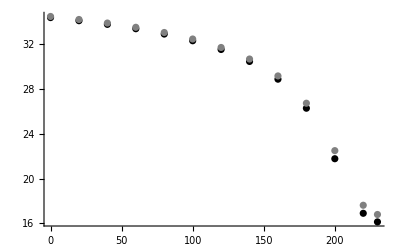

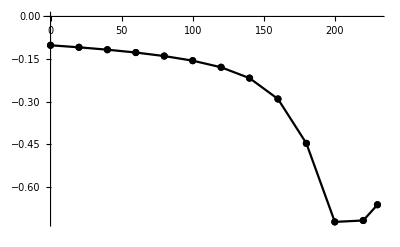

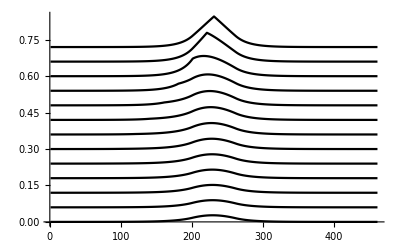

```mathematica
Show[
ListPlot[Table[{rd⟦i⟧,1000*elist3d⟦i⟧},{i,Length[rd]}],PlotRange->All,PlotStyle->Black],
ListPlot[Table[{rd⟦i⟧,1000*elist2d⟦i⟧},{i,Length[rd]}],PlotRange->All,PlotStyle-> Gray]
,PlotRange->All]

ListPlot[Table[{rd⟦i⟧,1000*(elist3d⟦i⟧-elist2d⟦i⟧)},{i,Length[rd]}],PlotRange->All,PlotStyle->Black,Joined->True,Mesh-> Full]
plot=0.0*rd;

Do[plot⟦i⟧=ListLinePlot[2*Exp[-Abs[z-rd⟦i⟧]/bohrrad3d⟦i⟧]*wavefn3d⟦i⟧+0.06*(i-1),PlotRange->All,PlotStyle-> Black]
,{i,Length[rd]}]

Do[plot⟦i⟧=ListLinePlot[ⅇ^(-Abs[z-rd⟦i⟧]/bohrrad3d⟦i⟧)*wavefn3d⟦i⟧+0.06*(i-1),PlotRange->All,PlotStyle-> Black]
,{i,Length[rd]}]
Show[plot,PlotRange->All]
```

## Binding Energy Variable Width

```mathematica
ClearAll["Global`*"]

t1=AbsoluteTime[];
wellist=Join[Range[10.,60.,10.],{80.,100.},Range[140.,220.,40.]];
dz=1.;
border=200.;
hom=7.62559/0.067;
ϵ=13.18*55.26349406*10^-4;
xlist={0.1,0.2,0.3};

ψmax=100.;
tol=10^-10;
elist3d=wavefn3d=bohrrad3d=ConstantArray[0.0*wellist,Length[xlist]];
 
i1[λ_,z_]:=π (λ Abs[z]+λ^2/2.) * Exp[-2. Abs[z]/λ];
i2[λ_,z_]:=-π*(z)*Exp[-2. Abs[z]/λ];
i3[λ_,z_]:= π (Abs[z]/λ-3./2. )*Exp[-2. Abs[z]/λ];
i4[λ_,z_]:=π λ *Exp[-2. Abs[z]/λ];


Do[
x=xlist⟦j⟧;
Do[
well=wellist⟦k⟧;

lw=Floor[well/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well,dz];lz=Length[z];
rd=border+0.5*well;
vmax=0.67*1.247*x;
v=0.0*z;
v⟦Range[lb]⟧=v⟦-Range[lb]⟧=vmax;
λ=100.;dλ=-1.;


α=i1[λ,z-rd];
β= 2.*i2[λ,z-rd];
i3λ=i3[λ,z-rd];
i4λ=i4[λ,z-rd];

energy=-0.030;de=0.0001;
γ=i3λ+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);
ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i<lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy1=energy-de;

λ+=dλ;

α=i1[λ,z-rd];
β= 2.*i2[λ,z-rd];
i3λ=i3[λ,z- rd];
i4λ=i4[λ,z- rd];

energy=-0.030;de=0.0001;
γ=i3λ+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy2=energy-de;

energy=energylast= Min[{energy1,energy2}];
If[energy2>energy1, dλ*=-1;λ+=dλ];

While[energy≤energylast && λ <200.,
energylast=energy;
λ+=dλ;

α=i1[λ,z-rd];
β= 2.*i2[λ,z-rd];
i3λ=i3[λ,z- rd];
i4λ=i4[λ,z- rd];

energy=-0.030;de=0.0001;
γ=i3λ+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧)
;i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy=energy-de;
];


elist3d⟦j,k⟧=energylast;
bohrrad3d⟦j,k⟧=λ-dλ;
wavefn3d⟦j,k⟧=ψ/(√(ψ.ψ dz));

,{k,Length[wellist]}];
,{j,Length[xlist]}];
t2=AbsoluteTime[];

(t2-t1)/60.
```

28.2547

## Without Donor

```mathematica
well=Join[Range[10.,60.,10.],{80.,100.},Range[140.,220.,40.]];
x={0.1,0.2,0.3};
enground=ConstantArray[0.0*well,Length[x]];
 hom=7.62559/0.067;

Do[
vmax=0.67*1.247*x⟦k⟧;
dz=1;border=200.;
lw=Floor[well⟦j⟧/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well⟦j⟧,dz];lz=Length[z];
rd = border+0.5*well⟦j⟧;

v=0.0*z;
v⟦Range[lb]⟧=v⟦-Range[lb]⟧=vmax;
H=ConstantArray[0,{lz,lz}];
c=-hom/(2*dz^2);b=hom/dz^2+v;

H⟦1,{1,2}⟧ = {b⟦1⟧,c};
H⟦-1,{-1,-2}⟧ = {b⟦-1⟧,c};
Do[H⟦i,{i-1,i,i+1}⟧ = {c,b⟦i⟧,c};,{i,2,lz-1}];

enground⟦k,j⟧=Sort[Eigenvalues[H]]⟦1⟧;
,{j,Length[well]},{k,Length[x]}]
```

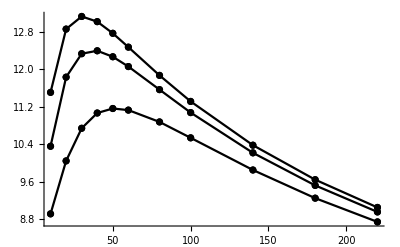

```mathematica
Show[
ListPlot[Table[{well⟦i⟧,1000*Abs[(elist3d⟦1,i⟧-enground⟦1,i⟧)]},{i,Length[well]}],PlotStyle->Black,Joined->True,Mesh->Full],
ListPlot[Table[{well⟦i⟧,1000*Abs[(elist3d⟦2,i⟧-enground⟦2,i⟧)]},{i,Length[well]}],PlotStyle->Black,Joined->True,Mesh->Full],
ListPlot[Table[{well⟦i⟧,1000*Abs[(elist3d⟦3,i⟧-enground⟦3,i⟧)]},{i,Length[well]}],PlotStyle->Black,Joined->True,Mesh->Full],
PlotRange->All
]
```

```mathematica
ClearAll["Global`*"]

t1=AbsoluteTime[];
wellist={240.,280.,320.,400.,500.,600.,800.,1000.};
dz=1.;
border=200.;
hom=7.62559/0.067;
ϵ=13.18*55.26349406*10^-4;
x=0.1;

ψmax=100.;
tol=10^-10;
elist3d=wavefn3d=bohrrad3d=0.0*wellist;
 
i1[λ_,z_]:=π (λ Abs[z]+λ^2/2.) * Exp[-2. Abs[z]/λ];
i2[λ_,z_]:=-π*(z)*Exp[-2. Abs[z]/λ];
i3[λ_,z_]:= π (Abs[z]/λ-3./2. )*Exp[-2. Abs[z]/λ];
i4[λ_,z_]:=π λ *Exp[-2. Abs[z]/λ];


Do[
well=wellist⟦k⟧;

lw=Floor[well/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well,dz];lz=Length[z];
rd=border+0.5*well;
vmax=0.67*1.247*x;
v=0.0*z;
v⟦Range[lb]⟧=v⟦-Range[lb]⟧=vmax;
λ=100.;dλ=-1.;


α=i1[λ,z-rd];
β= 2.*i2[λ,z-rd];
i3λ=i3[λ,z-rd];
i4λ=i4[λ,z-rd];

energy=-0.030;de=0.0001;
γ=i3λ+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);
ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i<lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy1=energy-de;

λ+=dλ;

α=i1[λ,z-rd];
β= 2.*i2[λ,z-rd];
i3λ=i3[λ,z- rd];
i4λ=i4[λ,z- rd];

energy=-0.030;de=0.0001;
γ=i3λ+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy2=energy-de;

energy=energylast= Min[{energy1,energy2}];
If[energy2>energy1, dλ*=-1;λ+=dλ];

While[energy≤energylast && λ <200.,
energylast=energy;
λ+=dλ;

α=i1[λ,z-rd];
β= 2.*i2[λ,z-rd];
i3λ=i3[λ,z- rd];
i4λ=i4[λ,z- rd];

energy=-0.030;de=0.0001;
γ=i3λ+2./hom*1/(4.π*ϵ)*i4λ-2./hom*α*(v-energy);

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧);
i++];
ψl=ψ⟦i⟧;
energy+=de;

While[Abs[de]>tol,
γ+=2./hom*α*de;

ψ=0.0*z;
ψ⟦1⟧=0;ψ⟦2⟧=10^-5;
i=2;
While[Abs[ψ⟦i⟧]<ψmax && i< lz,
ψ⟦i+1⟧=(1+β⟦i⟧/(2.α⟦i⟧)*dz)^-1*((-1+β⟦i⟧/(2.α⟦i⟧)*dz)ψ⟦i-1⟧+(2.-dz^2*γ⟦i⟧/α⟦i⟧)*ψ⟦i⟧)
;i++];
If[ψ⟦i⟧*ψl<0,de=-de/2.];
ψl=ψ⟦i⟧;energy+=de];
energy=energy-de;
];


elist3d⟦k⟧=energylast;
bohrrad3d⟦k⟧=λ-dλ;
wavefn3d⟦k⟧=ψ/(√(ψ.ψ dz));

,{k,Length[wellist]}];
t2=AbsoluteTime[];

(t2-t1)/60.
```

1.30717

## Without Donor

```mathematica
well={240.,280.,320.,400.,500.,600.,800.,1000.};
x=0.1;
enground=0.0*well;
 hom=7.62559/0.067;

Do[
vmax=0.67*1.247*x;
dz=1;border=200.;
lw=Floor[well⟦j⟧/dz];lb=Floor[border/dz];
z=Range[0.,2*border+well⟦j⟧,dz];lz=Length[z];
rd = border+0.5*well⟦j⟧;

v=0.0*z;
v⟦Range[lb]⟧=v⟦-Range[lb]⟧=vmax;
H=ConstantArray[0,{lz,lz}];
c=-hom/(2*dz^2);b=hom/dz^2+v;

H⟦1,{1,2}⟧ = {b⟦1⟧,c};
H⟦-1,{-1,-2}⟧ = {b⟦-1⟧,c};
Do[H⟦i,{i-1,i,i+1}⟧ = {c,b⟦i⟧,c};,{i,2,lz-1}];

enground⟦j⟧=Sort[Eigenvalues[H]]⟦1⟧;
,{j,Length[well]}]
```

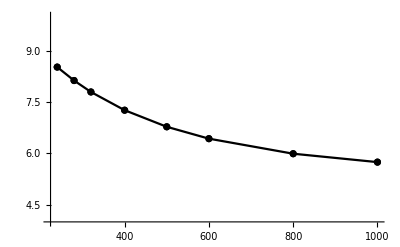

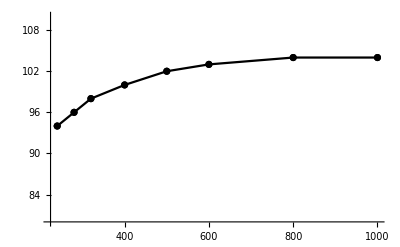

```mathematica
ListPlot[Table[{well⟦i⟧,1000*Abs[(elist3d⟦i⟧-enground⟦i⟧)]},{i,Length[well]}],PlotStyle->Black,Joined->True,Mesh->Full,PlotRange->{4,10}]
ListPlot[Table[{well⟦i⟧,bohrrad3d⟦i⟧},{i,Length[well]}],PlotStyle->Black,Joined->True,Mesh->Full,PlotRange->{80,110}]
```